```mathematica
(*Profil SPA*)
```

## -Graphics-

d250=0.23655+0.0104964 x-1.34946×10^-6 x^2

d200=0.131047+0.00785693 x-8.28067×10^-7 x^2

d160=0.105619+0.00568988 x-5.53784×10^-7 x^2

d125=0.137733+0.00380715 x-3.77028×10^-7 x^2

d112=0.116034+0.00308645 x-2.91316×10^-7 x^2

d90=0.0575015+0.00192277 x-2.14491×10^-7 x^2

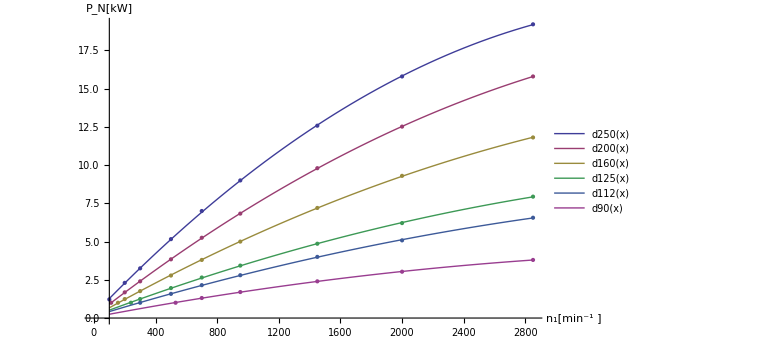

```mathematica
(*Odredjivanje nominalne specificne snage jednog uskog remena Pn*)
(*Definisanje uredjene liste podataka*)
Lista250={{100,1.22},{200,2.3},{300,3.25},{500,5.16},{700,7},{950,9},{1450,12.58},{2000,15.8},{2850,19.21}};
Lista200={{111.8,1},{200,1.68},{300,2.4},{500,3.84},{700,5.25},{950,6.83},{1450,9.8},{2000,12.52},{2850,15.8}};
Lista160={{156,1},{200,1.24},{300,1.76},{500,2.78},{700,3.8},{950,5},{1450,7.2},{2000,9.3},{2850,11.81}};
Lista125={{240,1},{300,1.24},{500,1.96},{700,2.65},{950,3.43},{1450,4.86},{2000,6.21},{2850,7.94}};
Lista112={{300,1},{500,1.58},{700,2.15},{950,2.8},{1450,4},{2000,5.08},{2850,6.56}};
Lista90={{530,1},{700,1.31},{950,1.7},{1450,2.4},{2000,3.03},{2850,3.8}};

(*Fitovanje*)
d250[x_]=Fit[Lista250,{1,x,x^2},x];
Print["d250=", d250[x]]
d200[x_]=Fit[Lista200,{1,x,x^2},x];
Print["d200=", d200[x]]
d160[x_]=Fit[Lista160,{1,x,x^2},x];
Print["d160=", d160[x]]
d125[x_]=Fit[Lista125,{1,x,x^2},x];
Print["d125=", d125[x]]
d112[x_]=Fit[Lista112,{1,x,x^2},x];
Print["d112=", d112[x]]
d90[x_]=Fit[Lista90,{1,x,x^2},x];
Print["d90=", d90[x]]

(*Stampanje funkcije*)
Grafik1=ListPlot[{Lista250,Lista200,Lista160,Lista125,Lista112,Lista90},AxesOrigin->{100,0},AxesLabel->{"n_1[min^-1 ]","P_N[kW]"}];
Grafik2=Plot[{d250[x],d200[x],d160[x],d125[x],d112[x],d90[x]},{x,100,2850},PlotLegends->"Expressions"];
Show[Grafik1,Grafik2]
```

```mathematica
(*Provera*)
d125[950]
```

3.41426